```mathematica
tasks := {
    Sin[2 * x ^ 3] ^ 2 / x ^ 3,
    (x ^ 2 - 4) * Sin[(Pi * (x ^ 2)) / 6] / (x ^ 2 - 1),
    Sqrt[Abs[3 * x ^ 3 + 2 * x ^ 2 - 10 * x]] / (4 * x),
    1 / 2 * Log[Sqrt[x ^ 2 + 1] / Sqrt[x ^ 2 - 1]] - 15 * x ^ 2,
    (x ^ 3 - x ^ 2 - x + 1) ^ (1 / 3) / Tan[x],
    2 * Log[(x - 1) / x] + 1,
    Log[x - 1] / (x - 1) ^ 2
}
```

```mathematica
getVariantForNumber[number_, variationsQuo_]:=(
    Module[{t},
        t = Mod[number , variationsQuo];
        If[t ≠ 0
                , t
                , variationsQuo
            ]
    ]
)
```

```mathematica
yourNumber := 2
numberOfYourTask := getVariantForNumber[yourNumber, Length[tasks]]
Print["Number of your task: ", numberOfYourTask]
```

Number of your task: 2

```mathematica
f[y_] := tasks[[numberOfYourTask ]] /. x -> y; 
f[x]
Plot[f[x], {x, -10, 10}]
```

((-4+x^2) Sin[(π x^2)/6])/(-1+x^2)

-Graphics-

```mathematica
u[x] := x ^ 2 - 1
rootsNull := Solve[u[x] == 0, x]
rootsNull
```

{{x→-1},{x→1}}

```mathematica
v := y[x] - y[-x]
Print["y(x) - y(-x) = ", v]
```

y(x) - y(-x) = -y[-x]+y[x]

```mathematica
Print["T = ", FunctionPeriod[y[x], x]]
```

T = 0

```mathematica
rootsAll := Reduce[y[x] == 0, x]
rootsAll
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[y[x]==0,x]

```mathematica
roots0 := List[
    {x -> -2},
    {x -> -1},
    {x -> 0},
    {x -> 1},
    {x -> 2},
    FindRoot[y[x] == 0, {x, 2.3}],
    FindRoot[y[x] == 0, {x, 3.4}]
]
x1 := -2
x2 := -1
x3 := 0
x4 := 1
x5 := 2
x6 := 2.44949
x7 := 3.4641
roots0
```

{{x→-2},{x→-1},{x→0},{x→1},{x→2},FindRoot[y[x]==0,{x,2.3}],FindRoot[y[x]==0,{x,3.4}]}

```mathematica
Print["y(0) = ", y[0]]
```

y(0) = ((-4+y^2) Sin[(π y^2)/6])/(-1+y^2)

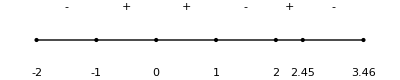

```mathematica
margin := 0.2
Show[
    Graphics[Line[{{x1, 0}, {x7, 0}}]],
    Graphics[Point[{x1, 0}, VertexColors->Red]],
    Graphics[Text["-2", {x1, -margin}]],
    Graphics[Point[{x2, 0}, VertexColors->Red]],
    Graphics[Text["-1", {x2, -margin}]],
    Graphics[Point[{x3, 0}, VertexColors->Red]],
    Graphics[Text["0", {x3, -margin}]],
    Graphics[Point[{x4, 0}, VertexColors->Red]],
    Graphics[Text["1", {x4, -margin}]],
    Graphics[Point[{x5, 0}, VertexColors->Red]],
    Graphics[Text["2", {x5, -margin}]],
    Graphics[Point[{x6, 0}, VertexColors->Red]],
    Graphics[Text["2.45", {x6, -margin}]],
    Graphics[Point[{x7, 0}, VertexColors->Red]],
    Graphics[Text["3.46", {x7, -margin}]],
    Graphics[Text["-", {(x1 + x2) / 2, margin}]],
    Graphics[Text["+", {(x2 + x3) / 2, margin}]],
    Graphics[Text["+", {(x3 + x4) / 2, margin}]],
    Graphics[Text["-", {(x4 + x5) / 2, margin}]],
    Graphics[Text["+", {(x5 + x6) / 2, margin}]],
    Graphics[Text["-", {(x6 + x7) / 2, margin}]]
]
```

```mathematica
dy := D[y[x], x]
dy==0
```

(π x (-4+x^2) Cos[(π x^2)/6])/(3 (-1+x^2))-(2 x (-4+x^2) Sin[(π x^2)/6])/((-1+x^2)^2)+(2 x Sin[(π x^2)/6])/(-1+x^2)==0

```mathematica
Plot[dy /. x -> z, {z, -10, 10}]
```

-Graphics-

```mathematica
FindRoot[dy == 0, {x, -3.1}]
dx1 := -3.04156
FindRoot[dy == 0, {x, -2.3}]
dx2 := -2.21885
dx3 := -1
FindRoot[dy == 0, {x, -0.1}]
dx4 := 0
dx5 := 1
FindRoot[dy == 0, {x, 2.2}]
dx6 := 2.21885
FindRoot[dy == 0, {x, 3.0}]
dx7 := 3.04156
```

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {-3.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {-3.1}.

FindRoot[dy==0,{x,-3.1}]

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {-2.3}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {-2.3}.

FindRoot[dy==0,{x,-2.3}]

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {-0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {-0.1}.

FindRoot[dy==0,{x,-0.1}]

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {2.2}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {2.2}.

FindRoot[dy==0,{x,2.2}]

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {3.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {dy} is not a list of numbers with dimensions {1} at {x} = {3.}.

FindRoot[dy==0,{x,3.}]

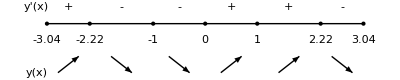

```mathematica
margin := 0.2
Show[
    Graphics[Line[{{dx1, 0}, {dx7, 0}}]],
    Graphics[Point[{dx1, 0}, VertexColors->Red]],
    Graphics[Text["-3.04", {dx1, -margin}]],
    Graphics[Point[{dx2, 0}, VertexColors->Red]],
    Graphics[Text["-2.22", {dx2, -margin}]],
    Graphics[Point[{dx3, 0}, VertexColors->Red]],
    Graphics[Text["-1", {dx3, -margin}]],
    Graphics[Point[{dx4, 0}, VertexColors->Red]],
    Graphics[Text["0", {dx4, -margin}]],
    Graphics[Point[{dx5, 0}, VertexColors->Red]],
    Graphics[Text["1", {dx5, -margin}]],
    Graphics[Point[{dx6, 0}, VertexColors->Red]],
    Graphics[Text["2.22", {dx6, -margin}]],
    Graphics[Point[{dx7, 0}, VertexColors->Red]],
    Graphics[Text["3.04", {dx7, -margin}]],
    Graphics[Text["y'(x)", {dx1 - margin, margin}]],
    Graphics[Text["y(x)", {dx1 - margin, -3 * margin}]],
    Graphics[Text["+", {(dx1 + dx2) / 2, margin}]],
    Graphics[Arrow[{{(dx1 + dx2) / 2 - margin, -3 * margin}, {(dx1 + dx2) / 2 + margin, -2 * margin}}]],
    Graphics[Text["-", {(dx2 + dx3) / 2, margin}]],
    Graphics[Arrow[{{(dx2 + dx3) / 2 - margin, -2 * margin}, {(dx2 + dx3) / 2 + margin, -3 * margin}}]],
    Graphics[Text["-", {(dx3 + dx4) / 2, margin}]],
    Graphics[Arrow[{{(dx3 + dx4) / 2 - margin, -2 * margin}, {(dx3 + dx4) / 2 + margin, -3 * margin}}]],
    Graphics[Text["+", {(dx4 + dx5) / 2, margin}]],
    Graphics[Arrow[{{(dx4 + dx5) / 2 - margin, -3 * margin}, {(dx4 + dx5) / 2 + margin, -2 * margin}}]],
    Graphics[Text["+", {(dx5 + dx6) / 2, margin}]],
    Graphics[Arrow[{{(dx5 + dx6) / 2 - margin, -3 * margin}, {(dx5 + dx6) / 2 + margin, -2 * margin}}]],
    Graphics[Text["-", {(dx6 + dx7) / 2, margin}]],
    Graphics[Arrow[{{(dx6 + dx7) / 2 - margin, -2 * margin}, {(dx6 + dx7) / 2 + margin, -3 * margin}}]]
]
```

```mathematica
Print["y''(-3.04) = ", D[y[x], x, x] /. x -> dx1, " => minimum, y(-3.04) = ", y[x] /. x -> dx1]
Print["y''(-2.22) = ", D[y[x], x, x] /. x -> dx2, " => maximum, y(-2.22) = ", y[x] /. x -> dx2]
Print["y''(0) = ", D[y[x], x, x] /. x -> dx4, " => minimum, y(0) = ", y[x] /. x -> dx4]
Print["y''(2.22) = ", D[y[x], x, x] /. x -> dx6, " => maximum, y(-2.22) = ", y[x] /. x -> dx6]
Print["y''(3.04) = ", D[y[x], x, x] /. x -> dx7, " => minimum, y(3.04) = ", y[x] /. x -> dx7]
```

y''(-3.04) = y''[-3.04156] => minimum, y(-3.04) = y[-3.04156]

y''(-2.22) = y''[-2.21885] => maximum, y(-2.22) = y[-2.21885]

y''(0) = y''[0] => minimum, y(0) = y[0]

y''(2.22) = y''[2.21885] => maximum, y(-2.22) = y[2.21885]

y''(3.04) = y''[3.04156] => minimum, y(3.04) = y[3.04156]

```mathematica
Print["lim [x -> -1 + 0] y(x) = ", Limit[y[x], x -> -1, Direction -> "FromAbove"]]
Print["lim [x -> -1 - 0] y(x) = ", Limit[y[x], x -> -1, Direction -> "FromBelow"]]
```

lim [x -> -1 + 0] y(x) = lim_(x→(-1)^+) y[x]

lim [x -> -1 - 0] y(x) = lim_(x→(-1)^-) y[x]

```mathematica
Print["lim [x -> 1 + 0] y(x) = ", Limit[y[x], x -> 1, Direction -> "FromAbove"]]
Print["lim [x -> 1 - 0] y(x) = ", Limit[y[x], x -> 1, Direction -> "FromBelow"]]
```

lim [x -> 1 + 0] y(x) = lim_(x→1^+) y[x]

lim [x -> 1 - 0] y(x) = lim_(x→1^-) y[x]

```mathematica
Print["lim [x -> +Infinity] y(x) = ", Limit[y[x], x -> +Infinity]]
Print["lim [x -> -Infinity] y(x) = ", Limit[y[x], x -> -Infinity]]
```

lim [x -> +Infinity] y(x) = lim_(x→∞) y[x]

lim [x -> -Infinity] y(x) = lim_(x→-∞) y[x]

```mathematica
Show[
    Plot[f[x], {x, -10, 10}],
    Graphics[{Dashing[{.05}], Line[{{-1, -10}, {-1, 10}}]}],
    Graphics[{Dashing[{.05}], Line[{{1, -10}, {1, 10}}]}]
]
```

-Graphics-